```mathematica
(* # 1 *)

(* Volume of T *)
Integrate[Integrate[Integrate[1,{z,0,1-x-y}],{y,0,1-x}],{x,0,1}]
```

1/6

```mathematica
(* Volume of T _2*)
ℛ=Tetrahedron[{{0,0,0},{1,0,0},{0,1,0},{0,0,1}}];
Volume[ℛ]
```

1/6

```mathematica
Graphics3D[ℛ]
```

-Graphics3D-

```mathematica
(* Area of face 1 *)
ℛ= Triangle[{{0,0,0},{0,1,0},{0,0,1}}];
Area[ℛ]
```

1/2

```mathematica
Graphics3D[ℛ]
```

-Graphics3D-

```mathematica
(* Area of face 2 *)
ℛ= Triangle[{{0,0,0},{1,0,0},{0,1,0}}];
Area[ℛ]
```

1/2

```mathematica
Graphics3D[ℛ]
```

-Graphics3D-

```mathematica
(* Area of face 3 *)
ℛ= Triangle[{{0,0,0},{1,0,0},{0,0,1}}];
Area[ℛ]
```

1/2

```mathematica
Graphics3D[ℛ]
```

-Graphics3D-

```mathematica
ℛ= Triangle[{{1,0,0},{0,1,0},{0,0,1}}];
Area[ℛ]
```

(√3)/2

```mathematica
(√3)/2
```

```mathematica
Graphics3D[ℛ]
(* # 2 *)
```

-Graphics3D-

```mathematica
L = 1;
f[x_]:=-x*Boole[0<x<L];
Integrate[-x*Sin[n*Pi*x],{x,0,1}]
```

(n π Cos[n π]-Sin[n π])/(n^2 π^2)

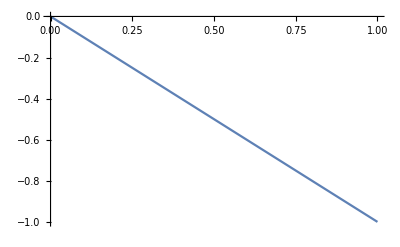

```mathematica
Plot[f[x],{x,0,1}]
```

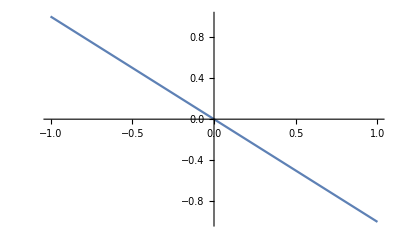

```mathematica
(* Odd Extension *)
Plot[-x, {x,-1,1}]
```

```mathematica
b[n_]:=(n π Cos[n π]-Sin[n π])/(n^2 π^2)
```

```mathematica
Table[b[n],{n,1,4,1}]
```

{-1/π,1/(2 π),-1/(3 π),1/(4 π)}

```mathematica
F[x_,n_]:=b[n]*Sin[n*Pi*x]
```

```mathematica
Table[F[x,n],{n,1,4,1}]
```

{-Sin[π x]/π,Sin[2 π x]/(2 π),-Sin[3 π x]/(3 π),Sin[4 π x]/(4 π)}

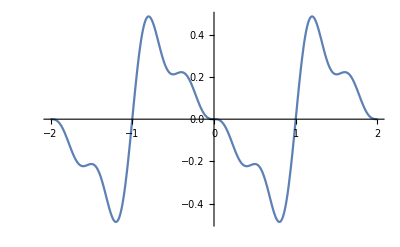

```mathematica
Plot[{F[x,1]+F[x,2]+F[x,3]+F[x,4]},{x,-2,2}]
```

```mathematica
(* # 4 *)
```

```mathematica
2*Integrate[(Sin[Pi*x]*Sin[n*Pi*x]),{x,0,1}]
```

(2 Sin[n π])/(π-n^2 π)

```mathematica
2*Integrate[(Sin[3*Pi*x]*Sin[n*Pi*x]),{x,0,1}]
```

(6 Sin[n π])/(9 π-n^2 π)

```mathematica
2*Integrate[(Sin[3*Pi*x]-Sin[Pi*x]*Exp[n*Pi])Sin[n*Pi*x],{x,0,1}]/(Exp[-n*Pi]-Exp[n*Pi])
```

(2 (ⅇ^(n π)/((-1+n^2) π)+3/(9 π-n^2 π)) Sin[n π])/(ⅇ^(-n π)-ⅇ^(n π))

```mathematica
B[n_]:= (2 (ⅇ^(n π)/((-1+n^2) π)+3/(9 π-n^2 π)) Sin[n π])/(ⅇ^(-n π)-ⅇ^(n π));
A[n_]:= (2 Sin[n π])/(π-n^2 π) - B[n];
u[x_,y_]:=Sum[Sin[n*Pi*x]*(A[n]*Exp[y*n*Pi] + B[n]*Exp[-y*n*Pi]),{n,1.00000000001,21.00000000000001,1}]
```

```mathematica
Plot3D[u[x,y],{x,0,1},{y,0,1},PlotStyle->Directive[Opacity[0.9]], PlotRange->{-1,1},Boxed->False]
```

-Graphics3D-

```mathematica
f[x_]:= Sin[Pi*x];
g[x_]:=Sin[3*Pi*x];
B[n_]:=2*NIntegrate[(g[x]-f[x]*Exp[n*Pi])Sin[n*Pi*x],{x,0,1}]/(Exp[-n*Pi]-Exp[n*Pi]);
A[n_]:=2*NIntegrate[f[x]*Sin[n*Pi*x],{x,0,1}]-B[n];
u[x_,y_]:=NSum[Sin[n*Pi*x]*(A[n]*Exp[y*n*Pi] + B[n]*Exp[-y*n*Pi]),{n,1,10,1}];
Plot3D[u[x,y],{x,0,1},{y,0,1},PlotPoints->25,PlotStyle->Directive[Opacity[0.72]], PlotRange->{-1.5,1.5},Boxed->False]
```

NIntegrate::inumr: The integrand Sin[π x] Sin[n π x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand (-ⅇ^(n π) Sin[π x]+Sin[3 π x]) Sin[n π x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[%107,Boxed->False]
```

-Graphics3D-

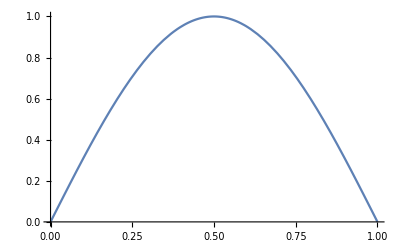

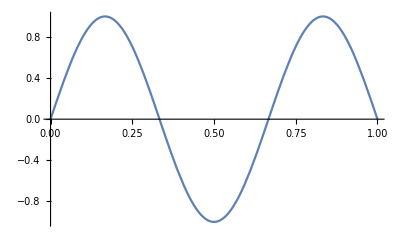

```mathematica
Plot[f[x],{x,0,1}]
Plot[g[x],{x,0,1}]
```

```mathematica
f[x_]:= Sin[Pi*x];
g[x_]:=Sin[3*Pi*x];
Plot3D[{f[x],g[x]},{x,0,1},{y,0,1}]

Plot3D[{((1-y)*f[x]),(y*g[x])},{x,0,1},{y,0,1}]

Plot3D[((1-y)*f[x])+(y*g[x]),{x,0,1},{y,0,1}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(* # 5 *)
```

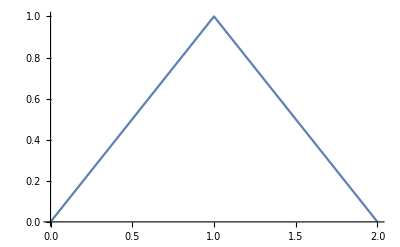

```mathematica
f[x_]:=1-Abs[x-1];
Plot[f[x],{x,0,2}]
```